## 0.1 Dataset

```mathematica
width = 0.003;(*мм*)
q = 10^-6;(*м^2/с*)
λ =10;(*Вт/(м*C)*)
τ1 = 50;(*C*)
τ2 = 20;(*C*)
α1 = 30;(*Вт/(м^2 К)*)
α2 = 10;(*Вт/(м^2 К)*)
n = 10;
t0=20;
dx = width / (n - 1)
export[name_, data_]:=Export["ММиАвАП\\lab3\\"<>name<>".png", data]
```

0.000333333

## 1.1 Steady

```mathematica
FormTemperatures[n_] := Table[Symbol["$t"<>ToString@i],{i,n}];

(*equations*)
FormInnerEq[prev_,cur_,next_]:=Function[(next-2*cur+prev)/dx^2==0][prev,cur,next];
FormEdgeEq1[cur_,next_]:=Function[(next-cur)/dx+α1*(τ1-cur)==0][cur];
FormEdgeEq2[cur_,prev_]:=Function[-(cur-prev)/dx+α2*(τ2-cur)==0][cur];

(*creating system of equations*)
FormEqSystem[n_]:=Module[{equations={},t=FormTemperatures[n]},
AppendTo[equations, FormEdgeEq1[t[[1]],t[[2]]]];
For[i=2,i<n ,i++,AppendTo[equations,FormInnerEq[t[[i-1]],t[[i]],t[[i+1]]]]];
AppendTo[equations, FormEdgeEq2[t[[n]],t[[n-1]]]];
Return[equations];
];

(*calculated temperatues*)
FindTemps[n_]:=Module[{eqs = FormEqSystem[n], vars=FormTemperatures[n], result},
result = vars/.Solve[eqs,vars]
];
```

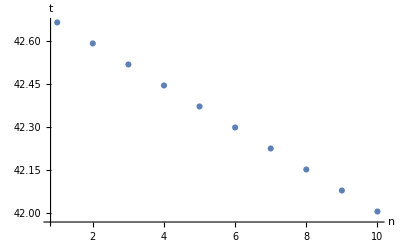

```mathematica
Module[{plot},
plot = ListPlot[FindTemps[n], PlotRange->Full, PlotMarkers->Automatic,AxesLabel->{"n","t"}];
export["steady",plot];
plot
]
```

## 1.2 Unsteady

#### Common

```mathematica
dt:= Module[{t=dx^2/(2q),n=0},
While[t<1, t=t*10;n++];
Return[dx^2/(2q)-(t*10^n-Floor[t*10^n])/10^n]]
nt = 50;

PlotNonStat[data_]:= ListPlot[data, PlotMarkers->Automatic, PlotRange->Full, AxesLabel->{"τ","t"},PlotLabels->Array[#&,n], PlotLabel->"τ = "<>ToString@(nt*dt)<>"c"]

(*matrix of variables*)
FormVars[m_, n_]:=Return[Table[Symbol["$t"<>ToString@i<>"x"<>ToString@j],{i,m}, {j, n}]];
```

#### Explicit

```mathematica
FindBorderT1[t_]:=Module[{root={}},
root=x/.Solve[(t-x)/dx+ α1*(τ1-x)==0,x];
Return[root[[1]]];
];
FindBorderT2[t_]:=Module[{root={}},
root=x/.Solve[(x-t)/dx+ α2*(τ2-x)==0,x];
Return[root[[1]]];
];

FindInnerT[left_,straight_,right_] := Module[{},Return[(q*dt*(right-2*straight+left)/dx^2)+straight]];

(*calculates temperatures*)
tExplicit[pts0_, tms0_] := Module[{temp={}, result = {},pts=pts0, tms=tms0,t=FormVars[pts0,tms0]},
For[i=1,i≤pts,i++,t[[i]][[1]]=t0];
For[j=2,j≤tms,j++,
For[i=2,i<pts,i++,t[[i]][[j]]=FindInnerT[t[[i-1]][[j-1]],t[[i]][[j-1]],t[[i+1]][[j-1]]];];
t[[1]][[j]]=FindBorderT1[t[[2]][[j]]];
t[[pts]][[j]]=FindBorderT2[t[[pts-1]][[j]]];
];
Return[t];
];
```

```mathematica
Module[{plot = PlotNonStat[tExplicit[n,nt]]},export["unsteady_explicit", plot];plot]
```

-Graphics-

#### Implicit

```mathematica
(*creates equation for init moment of time*)
FormInitTime[matr_,i_] := Function[matr[[i]][[1]]==t0][matr[[i]][[1]]]

(*creats border conditions equations*)
FormEdgeEq1NonStat[matr_,j_,a_,b_] := Function[(matr[[b]][[j]]-matr[[a]][[j]])/dx+ α1*(τ1-matr[[a]][[j]])==0][{matr[[b]][[j]],matr[[a]][[j]]}];
FormEdgeEq2NonStat[matr_,j_,a_,b_] := Function[-(matr[[b]][[j]]-matr[[a]][[j]])/dx+ α2*(τ2-matr[[b]][[j]])==0][{matr[[b]][[j]],matr[[a]][[j]]}];

(*creates equation for inner point*)
FormInnerEqImplicit[matr_,i_,j_] := Function[(matr[[i]][[j]] - matr[[i]][[j-1]])/dt == q(matr[[i+1]][[j]]-2matr[[i]][[j]]+matr[[i-1]][[j]])/dx^2][{matr[[i-1]][[j]],matr[[i]][[j]],matr[[i+1]][[j]],matr[[i]][[j-1]]}];

(*combines all equations*)
createImplicitEqs[vars_,pts0_, tms0_]:=Module[{equations ={}, pts=pts0, tms=tms0,t=vars},
For[i=1,i≤pts,i++,For[j=1,j≤tms,j++,
If[j==1,
(*adds equations for initial time*)
AppendTo[equations,FormInitTime[t,i]],
(*adds equations for all time moments, except initial*)
Switch[i,
(*adds border condition for the 1st point*)
1,AppendTo[equations,FormEdgeEq1NonStat[t,j,i,i+1]],
(*adds border condition for the last point*)
pts,AppendTo[equations,FormEdgeEq2NonStat[t,j,i-1,i]],
(*adds equation for inner point*)
_,AppendTo[equations,FormInnerEqImplicit[t,i,j]]
];
];
];
];
Return[equations];
];

(*calculates temperatures*)
tImplicit[pts0_, tms0_] := Module[{temp={}, result = {},pts=pts0, tms=tms0,t=FormVars[pts0,tms0]},
For[i=1,i≤pts,i++,For[j=1,j≤tms,j++,AppendTo[temp, t[[i]][[j]]]]];
result = temp /.Solve[createImplicitEqs[t,pts,tms], temp][[1]];
Return[ArrayReshape[result, {pts, tms}]]
];
```

```mathematica
Module[{plot = PlotNonStat[tImplicit[n,nt]]},export["unsteady_implicit", plot];plot]
```

-Graphics-

#### Comparison

```mathematica
compValue = 5000;
compValue*dt
PlotNonStatComp[data_,nt_]:= Show[ListPlot[data, PlotMarkers->Automatic, AxesLabel->{"τ","t"},PlotLabels->Array[#&,n], PlotLabel->"τ = "<>ToString@(nt*dt)<>"c"],Plot[y=τ1,{x,0,compValue}],Plot[y=τ2,{x,0,compValue}],PlotRange->{{0,compValue},{15,55}}];
imp = PlotNonStatComp[tImplicit[n,compValue],compValue]
exp = PlotNonStatComp[tExplicit[n,compValue],compValue]
export["implicit"<>ToString@compValue,imp];
export["explicit"<>ToString@compValue,exp];
```

250.

-Graphics-

-Graphics-